```mathematica
π^2/2.
```

4.9348

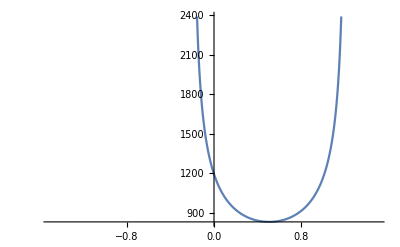

```mathematica
Block[{t=0.3530,a=0.0017,μ=0.2},Plot[1/(2t*a √(((μ+E)/t)-((μ+E)/(2t))^2))+1/(2t*a √(((μ+E)/t)-((μ+E)/(2t))^2)),{E,-1.5,1.5}]]
```

```mathematica
KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]//MatrixForm
```

(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)

```mathematica
ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]//MatrixForm
```

(ϵk | 0 | 0 | -Δ
0 | ϵk | Δ | 0
0 | Δ | -ϵk | 0
-Δ | 0 | 0 | -ϵk)

```mathematica
Eigensystem[ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]]
```

{{-√(Δ^2+ϵk^2),-√(Δ^2+ϵk^2),√(Δ^2+ϵk^2),√(Δ^2+ϵk^2)},{{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}}}

```mathematica
hbdg=ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+B*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]
```

{{B+ϵk,0,0,-Δ},{0,-B+ϵk,Δ,0},{0,Δ,-B-ϵk,0},{-Δ,0,0,B-ϵk}}

```mathematica
Eigensystem[ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+B*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]]
```

{{-B-√(Δ^2+ϵk^2),B-√(Δ^2+ϵk^2),-B+√(Δ^2+ϵk^2),B+√(Δ^2+ϵk^2)},{{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}}}

```mathematica
{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}/{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}//FullSimplify
```

Δ/(2 √(Δ^2+ϵk^2))

```mathematica
{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}/{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}//FullSimplify
```

Δ/(2 √(Δ^2+ϵk^2))

```mathematica
{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0}
```

(-ϵk-√(Δ^2+ϵk^2))/Δ

```mathematica
{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}.SparseArray[{{3,2}->-1,{4,1}->1},{4,4}].{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}
```

-(ϵk+√(Δ^2+ϵk^2))/Δ

```mathematica
{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}
```

1+((-ϵk+√(Δ^2+ϵk^2))^2)/Δ^2

```mathematica
Block[{Δ=1.008,t=0.353,μ=2,g=3},1/2 g*Δ/(2π)*NIntegrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),{ϕ,-π,π}]]
```

1.00796

```mathematica
delta[x_]:=Block[{Δ=x,t=0.352986576286180,μ=.3,g=1},1/2 g*Δ/(2π)*NIntegrate[1/(√(Δ^2+(2*t*(1-Cos[ϕ])-μ)^2)),{ϕ,-π,π}]]
```

```mathematica
FixedPoint[f,0.2]
```

0.289937

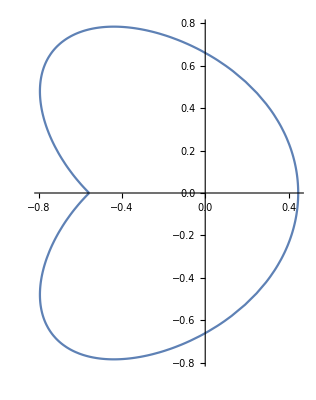

```mathematica
Block[{Δ=1.008,t=0.353,μ=2,g=3},PolarPlot[1/(√(Δ^2+(t*ϕ^2-μ)^2)),{ϕ,-π,π}]]
```

```mathematica
(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->π)-(Integrate[1/(√(Δ^2+(t*ϕ^2-μ)^2)),ϕ]/.ϕ->-π)//Simplify
```

-(2 ⅈ √(1+(ⅈ π^2 t)/(Δ-ⅈ μ)) √(1-(ⅈ π^2 t)/(Δ+ⅈ μ)) EllipticF[ⅈ ArcSinh[π √(-(ⅈ t)/(Δ+ⅈ μ))],-(Δ+ⅈ μ)/(Δ-ⅈ μ)])/(√(-(ⅈ t)/(Δ+ⅈ μ)) √(Δ^2+(-π^2 t+μ)^2))

```mathematica
(ArcTanh[(k √x)/(√(k^2 x+Δ^2-μ))]/(√x)/.k->u)-(ArcTanh[(k √x)/(√(k^2 x+Δ^2-μ))]/(√x)/.k->-u)
```

(2 ArcTanh[(u √x)/(√(u^2 x+Δ^2-μ))])/(√x)

```mathematica
Eigensystem[hbdg]
```

{{-B-√(Δ^2+ϵk^2),B-√(Δ^2+ϵk^2),-B+√(Δ^2+ϵk^2),B+√(Δ^2+ϵk^2)},{{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1},{0,-(-ϵk-√(Δ^2+ϵk^2))/Δ,1,0},{-(ϵk+√(Δ^2+ϵk^2))/Δ,0,0,1}}}

```mathematica
Hsc=Δ^2/g*V
```

```mathematica
1/2*({0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.hbdg.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}/{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}.{0,-(-ϵk+√(Δ^2+ϵk^2))/Δ,1,0}+{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.hbdg.{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}/{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1}.{-(ϵk-√(Δ^2+ϵk^2))/Δ,0,0,1})//Simplify
```

-((Δ^2+ϵk^2) (-ϵk+√(Δ^2+ϵk^2)))/(Δ^2+ϵk (ϵk-√(Δ^2+ϵk^2)))

```mathematica
Integrate[(Δ^2+(t ϕ^2-μ)^2)/(Δ^2/(t ϕ^2-μ-√(Δ^2+(t ϕ^2-μ)^2))+t ϕ^2-μ),{ϕ,0,π}]
```

$Aborted

```mathematica
hn=ϵk*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]+0*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+B*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]
```

{{B+ϵk,0,0,0},{0,-B+ϵk,0,0},{0,0,-B-ϵk,0},{0,0,0,B-ϵk}}

```mathematica
Eigensystem[hn]
```

{{-B-ϵk,B-ϵk,-B+ϵk,B+ϵk},{{0,0,1,0},{0,0,0,1},{0,1,0,0},{1,0,0,0}}}

```mathematica
1/2*(Sum[vec.hn.vec,{vec,{{0,0,1,0},{0,0,0,1}}}])
```

-ϵk

```mathematica
Block[{a=0.0017,Δ=1.0080,μ=2,hsc,ϵk,t=0.3530},hsc=-((Δ^2+ϵk^2) (-ϵk+√(Δ^2+ϵk^2)))/(Δ^2+ϵk (ϵk-√(Δ^2+ϵk^2)))+ϵk/.ϵk->t*(k*a)^2-μ;NIntegrate[hsc,{k,-π/a,π/a}]]
```

-9076.02

```mathematica
Block[{ϕn,ϕp,t=0.352986576286180,μ=0.3,Δ=0.289936776925109,g=1,B=0.1},ϕn=√((μ+B)/t);ϕp=√((μ-B)/t);{1/2*1/(2π)*2*(Integrate[(t*ϕ^2-μ)+B,{ϕ,0,ϕp}]+Integrate[-(t*ϕ^2-μ)-B,{ϕ,ϕp,π}]+Integrate[(t*ϕ^2-μ)-B,{ϕ,0,ϕn}]+Integrate[-(t*ϕ^2-μ)+B,{ϕ,0,ϕn}]),(1/π NIntegrate[(Δ^2+(t ϕ^2-μ)^2)/(Δ^2/(t ϕ^2-μ-√(Δ^2+(t ϕ^2-μ)^2))+t ϕ^2-μ),{ϕ,0,π}]+Δ^2/g)}]
```

{-0.512586,-0.987509}

```mathematica
0.289936776925109/√2
```

0.205016

```mathematica
f[g0_]:=Block[{ϕn,ϕp,t=0.352986576286180,μ=0.5,Δ,g=g0,B0,delta},delta[x_]:=Block[{Δ0=x},1/2 g*Δ0/(2π)*NIntegrate[1/(√(Δ0^2+(t*ϕ^2-μ)^2)),{ϕ,-π,π}]];Δ=FixedPoint[delta,g];B0=Δ/√2;ϕn=√((μ+B0)/t);ϕp=√((μ-B0)/t);{Δ,FindRoot[1/2*1/(2π)*2*(Integrate[(t*ϕ^2-μ)+B,{ϕ,0,ϕp}]+Integrate[-(t*ϕ^2-μ)-B,{ϕ,ϕp,π}]+Integrate[(t*ϕ^2-μ)-B,{ϕ,0,ϕn}]+Integrate[-(t*ϕ^2-μ)+B,{ϕ,ϕn,π}])-(1/π NIntegrate[(Δ^2+(t ϕ^2-μ)^2)/(Δ^2/(t ϕ^2-μ-√(Δ^2+(t ϕ^2-μ)^2))+t ϕ^2-μ),{ϕ,0,π}]+Δ^2/g),{B,B0}][[1,2]]}]
```

```mathematica
f[1]
```

{0.185275,0.132474}

```mathematica
flist=f/@Range[0.3,1.4,0.1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {1.19032}. NIntegrate obtained 32.3744 and 0.0000458812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {1.19032}. NIntegrate obtained 33.6009 and 0.000093955 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {ϕ} = {1.19646}. NIntegrate obtained 34.6504 and 0.000182955 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.000405042,0.000292675},{0.00365539,0.00258508},{0.0136742,0.0096717},{0.0328982,0.0232881},{0.0614,0.0435429},{0.0976587,0.069443},{0.139591,0.0995581},{0.185275,0.132474},{0.233267,0.167013},{0.282613,0.202285},{0.33274,0.237659},{0.383324,0.272705}}

```mathematica
flist[[All,1]]/flist[[All,2]]
```

{1.38393,1.41403,1.41384,1.41266,1.41011,1.40631,1.4021,1.39857,1.3967,1.3971,1.40007,1.40564}

```mathematica
Block[{ϕn,ϕp,t,μ,Δ,g,B},ϕn=√((μ+B)/t);ϕp=√((μ-B)/t);1/2*1/(2π)*2*(Integrate[(t*ϕ^2-μ)+B,{ϕ,0,ϕp}]+Integrate[-(t*ϕ^2-μ)-B,{ϕ,ϕp,π}]+Integrate[(t*ϕ^2-μ)-B,{ϕ,0,ϕn}]+Integrate[-(t*ϕ^2-μ)+B,{ϕ,ϕn,π}])]//FullSimplify
```

(-π^3 t+3 π μ+2 B (√((-B+μ)/t)-√((B+μ)/t))-2 μ (√((-B+μ)/t)+√((B+μ)/t)))/(3 π)

```mathematica
f[g0_,ed_,x_]:=Block[{(*g=5,*)g=g0,tx=3.7976,ty=3.7976,tz=3.7976,μ=11,Δ=x,Δ1,ED=ed*433*8.617333262*^-5,(*ED=50*433*8.617333262*^-5*)},Δ1=g/2*Δ/(2π)^3 NIntegrate[(1*HeavisideTheta[ED-√(Δ^2+(2tx (1-Cos[ϕx])+2ty (1-Cos[ϕy])+2tz (1-Cos[ϕz])-μ)^2)])/(√(Δ^2+(2tx (1-Cos[ϕx])+2ty (1-Cos[ϕy])+2tz (1-Cos[ϕz])-μ)^2)),{ϕx,-π,π},{ϕy,-π,π},{ϕz,-π,π}];Δ1]
```

```mathematica
Dynamic[{g0,ed}]
```

```mathematica
gap=ParallelTable[{g0,ed,Quiet@FixedPoint[f[g0,ed,#]&,0.002,SameTest->(Abs[#1-#2]<1*^-6&)]},{g0,6,7,0.1},{ed,50,50,10}]
```

$Aborted

```mathematica
f[2.7495*^-04]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 80.2748 and 9.65383 for the integral and error estimates.

0.000444901

```mathematica
f[%]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 60.4203 and 0.0819433 for the integral and error estimates.

0.117812

```mathematica
f/@Range[0.0001,0.01,0.001]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 80.1451 and 9.77206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 83.5921 and 9.24279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 82.7825 and 8.19516 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.00016155,0.00185348,0.00350419,0.00505775,0.00670616,0.0082418,0.00971697,0.0113607,0.0127002,0.0141624}

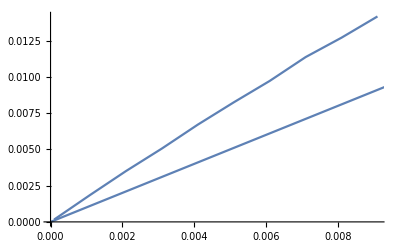

```mathematica
ListLinePlot[Transpose@{Range[0.0001,0.01,0.001],Out@34},Epilog->{ First@Plot[x,{x,0,0.01}]}]
```

```mathematica
f[0.0001]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 80.1451 and 9.77206 for the integral and error estimates.

0.00016155

```mathematica
f[%]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 80.2584 and 9.65246 for the integral and error estimates.

0.000422458